```mathematica
f[x_,Nobs_,Nbg_,Nsig_,NErr_]:=1/2(1+Erf[(Nbg+Nsig)/(√2 NErr)])CDF[PoissonDistribution[x],Nobs]PDF[NormalDistribution[Nbg+Nsig,NErr],x];
Pval[Nobs_,Nsig_,NErr_,Nbg_]:=NIntegrate[ f[x,Nobs,Nbg,Nsig,NErr],{x,0.,Infinity},MaxRecursion->20]
```

```mathematica
nobs=24;
nbg = 3.3;
nErr=1.5;
```

```mathematica
n0=Max[{0,nobs-nbg - 4 √(nbg + nErr^2)}];
n1=Max[{0,nobs-nbg + 4 √(nbg + nErr^2)}];
```

```mathematica
Pval[nobs,n0,nErr,nbg]
Pval[nobs,n1,nErr,nbg]
```

0.987065

0.0617521

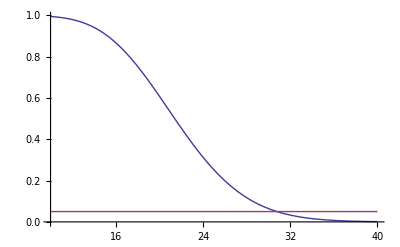

```mathematica
Plot[{Pval[nobs,x,nErr,nbg],0.05},{x,10.,40.}]
```